# Quantum Mechanics Final Project

Adiabatic Theorem Analysis

John Mercer

Introduction

To illustrate the adiabatic theorem in action, we will model a particle in a one dimensional infinite square well.

Recall we want to analyze the behavior of the quantum state as the time-dependent potential V(x, t) and therefore the Hamiltonian changes slowly in time.

** make a note about symbols and labels (i, n) e.g.

a. Problem Setup

Using problem 10.1 from page 370-371.

```mathematica
Clear["Global`*"];
```

```mathematica
VELOCITY=1; (* constant velocity of increasing well width *)
PSIINDEX = 1;(* index to select a specific solution *)
INITIALWIDTH = 1; (* this is 'a' in the book, the initial width of the well *)
ℏ=6.626 10^-34/2 Pi;
```

```mathematica
TIMELAPSE = 1; (* the amount of time to elapse *)
MASS=9.10938356 *10^-31;(* fixed mass *)
```

Instantaneous width as a function of velocity and time:

```mathematica
w[wa_, wv_, wt_]:=wa + wv * wt;
```

nth allowed energy of the original well of width=a:

```mathematica
EnergyLevel[en_,ea_, em_]:=Refine[(π^2 en^2 ℏ^2)/(2em ea^2),Element[en,Integers]];
```

Complete set of solutions:

```mathematica
Ψ[px_, pt_, pn_]:=
√(2/w[INITIALWIDTH,VELOCITY,pt])Sin[(pn π px)/w[INITIALWIDTH,VELOCITY,pt]] Exp[-(ⅈ (MASS VELOCITY px^2-2EnergyLevel[pn,INITIALWIDTH,MASS] INITIALWIDTH pt))/(2 ℏ w[INITIALWIDTH,VELOCITY,pt])];
```

Initial wave function at t=0:

```mathematica
Subscript[Ψ, 0][tempx_]:=√(2/INITIALWIDTH)Sin[π/INITIALWIDTH tempx];
```

b. Plotting the Wave Function and Probability

```mathematica
Manipulate[Plot[{Ψ[x,t,PSIINDEX]*Conjugate[Ψ[x, t ,PSIINDEX]],
Re[Ψ[x,t ,PSIINDEX]],
Im[Ψ[x,t,PSIINDEX]]},
{x,0,w[INITIALWIDTH,VELOCITY,t]},
PlotStyle->{{Black,Thickness[.005]},
		    {Blue,Thickness[.005]},
		    {Green,Thickness[.005]}},
PlotRange->Automatic
],
{t,0,TIMELAPSE ,Appearance->"Open"}
]
```

c. Plotting the Probability by State

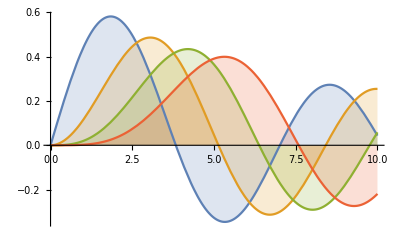

```mathematica
Plot[Evaluate[Table[BesselJ[bn,bx],{bn,4}]],{bx,0,10},Filling->Axis]
```

```mathematica
Manipulate[Plot[Evaluate[BesselJ[#,bx]&/@bn],
{bx,0,xmax},
Filling->Axis,
PlotRange->{{0,10},{-.7,.7}}
],
{{xmax,6},10.^-5,10,Appearance->"Open"},
{{bn,{1,3}},Range[5],TogglerBar}
]
```

```mathematica
prob[xx_, tt_, nn_] := Conjugate[Ψ[xx,tt, nn]] * Ψ[xx,tt, nn];
```

```mathematica
Manipulate[
Plot[Evaluate[prob[xparm, tparm, #] &/@ nparm],
	{xparm,0,2},
	Filling->Axis,
	PlotRange->{{0,2},{0,2}}
	],
{{tparm,10.^-5},0,TIMELAPSE,Appearance->"Open"},
{{nparm,{1}},Range[10],TogglerBar}
]
```

d. Analyzing the Expansion Coefficients

α is a dimensionless measure of the speed in which the well expands:

```mathematica
alpha[am_,av_,aa_]:=((am av aa)/(2 π^2 ℏ));
```

```mathematica
alpha[MASS,VELOCITY,INITIALWIDTH]
```

44.3392

The expansion coefficients c_n:

```mathematica
c[cn_,cm_,cv_,ca_]:=Refine[2/π∫_0^π Exp[- ⅈ alpha[cm,cv,ca] z^2]Sin[cn z]Sin[z]ⅆz,Element[cn,Integers]];
```

```mathematica
c[1,MASS,VELOCITY,INITIALWIDTH]
```

-0.000667891-0.000683139 ⅈ

```mathematica
cn[un_]:=Refine[2/π NIntegrate[ Exp[-ⅈ  alpha[MASS,VELOCITY,INITIALWIDTH] z^2]Sin[un z]Sin[z], {z, 0 , π}],Element[un,Integers]];
```

```mathematica
Re[Conjugate[cn[1]]*cn[1]]
```

9.12757×10^-7

```mathematica
Re[Conjugate[cn[2]]*cn[2]]
```

3.65145×10^-6

```mathematica
Re[Conjugate[c[1,MASS,VELOCITY,INITIALWIDTH]]*c[1,MASS,VELOCITY,INITIALWIDTH]]
```

9.12757×10^-7

d. Expressing the General Solution

```mathematica
Nmax=10;
Subscript[Ψ, g][gx_,gt_,nmax_]:=∑_(n=1)^nmax cn[n]Ψ[gx,gt, nmax];
```

```mathematica
Re[Subscript[Ψ, g][1,0.5,10]]
```

-0.00751762

```mathematica
Subscript[Ψ, g][0.5,0,10]*Conjugate[Subscript[Ψ, g][0.5,0,10]]
```

2.0018×10^-33+0. ⅈ

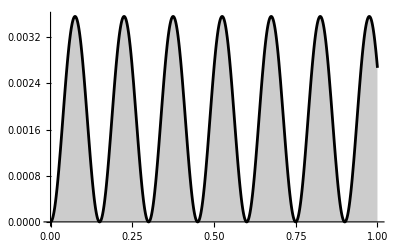

```mathematica
Plot[{Subscript[Ψ, g][xparm,0.5,10]*Conjugate[Subscript[Ψ, g][xparm,0.5,10]]},
{xparm,0,1},
Filling->Axis,
PlotRange->Full,
PlotStyle->{{Black,Thickness[.005]}}]
```